## Extremum-seeking control (Problem 10.6)

```mathematica
Clear["Global`*"];
```

Works but needs to use Cos, not Sin to prevent problem at t=0

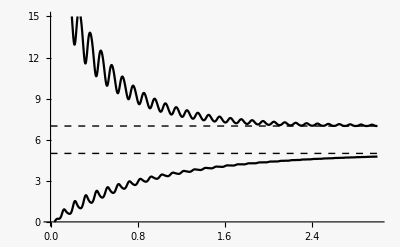

```mathematica
Clear["Global`*"];
pars={k->50,a->0.2,ω0->2π 10,ωh->2π ,j00->7,θ00->5,d0->0,ωd->2π 0.03};
j0[θ_,θ0_]:=j00+1/2(θ-θ0)^2/.pars;
θ0[t_]:=θ00+d0 Sin[ωd t]/.pars;
eqs={  θh'[t]==-k a Cos[ω0 t]η[t], 
	η'[t]==- ωh η[t]+ j'[t],
	j[t]== j0[θh[t]+a Cos[ω0 t],θ0[t]]};

init={θh[0]==0,η[0]==0};
tmax=3;
{θhs,ηs,js}=NDSolveValue[{eqs/.pars,init},{θh,η,j},{t,0,tmax}];
Plot[{js[t],θhs[t],θ0[t],j0[θ00,θ00]/.pars},{t,0,tmax},PlotRange->{0,15},PlotStyle->{Black,Black,{Black,Dashed,Thin},{Black,Dashed,Thin}}]
```

add periodic disturbance in θ[t]

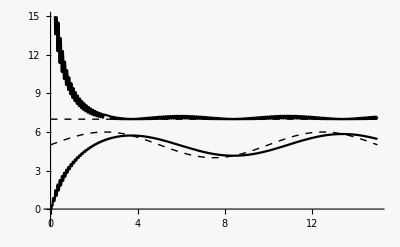

```mathematica
Clear["Global`*"];
pars={k->50,a->0.2,ω0->2π 10,ωh->2π ,j00->7,θ00->5,d0->1,ωd->2π 0.1 };
j0[θ_,θ0_]:=j00+1/2(θ-θ0)^2/.pars;
θ0[t_]:=θ00+d0 Sin[ωd t]/.pars;
eqs={  θh'[t]==-k a Cos[ω0 t]η[t], 
	η'[t]==- ωh η[t]+ j'[t],
	j[t]== j0[θh[t]+a Cos[ω0 t],θ0[t]]};

init={θh[0]==0,η[0]==0};
tmax=15;
{θhs,ηs,js}=NDSolveValue[{eqs/.pars,init},{θh,η,j},{t,0,tmax}];
Plot[{js[t],θhs[t],θ0[t],j0[θ00,θ00]/.pars},{t,0,tmax},PlotRange->{-1,15},PlotStyle->{Black,Black,{Black,Dashed,Thin},{Black,Dashed,Thin}}]
```

Export data

```mathematica
dt=0.01;
dat=Table[Through[{js,θhs}[t]],{t,0,tmax,dt}];
 (*
SetDirectory[NotebookDirectory[]];
Export["extremumSeekPlot.dat",dat]; 
*)
```